```mathematica
P[M2_,M_]:=Exp[-I π M/(4 k)((I M2+2λ)^2+4 λ^2)]
```

```mathematica
P[M2,M]P[M2,M]//Simplify
```

ⅇ^((M π (ⅈ M2^2+4 M2 λ-8 ⅈ λ^2))/(2 k))

```mathematica
{θ1->1/2 (Subscript[M, 1]+Subscript[M, 2]-M-k),θt->(M+k)/2,θoo->1/2 (i Subscript[ζ, 1]-i Subscript[ζ, 2]),t-> q^M1,q->E^((2π I)/k)}
```

{θ1→1/2 (M_1+M_2-M-k),θt→(M+k)/2,θoo→1/2 (i ζ_1-i ζ_2),t→q^M1,q→ⅇ^((2 ⅈ π)/k)}

```mathematica
ToExpression["\theta_\\infty=\\frac{i\\zeta_1-i\\zeta_2}{2}",TeXForm,HoldForm]
```

h e t a_∞==1/2 (i ζ_1-i ζ_2)

```mathematica
\theta_1=\frac{M_1+M_2-M-k}{2},\quad
		\theta_t=\frac{M+k}{2},\quad
		\theta_\infty=\frac{i\zeta_1-i\zeta_2}{2},\quad
		\frac{\log t}{\log\mathfrak{q}}=M_1.
```

```mathematica
Series[(M π (ⅈ M2^2+4 M2 λ-8 ⅈ λ^2))/(2 k),{λ,0,3}]
```

(ⅈ M M2^2 π)/(2 k)+(2 M M2 π λ)/k-(4 ⅈ M π λ^2)/k+O[λ]^4

```mathematica
{θ1->1/2 (Subscript[M, 1]+Subscript[M, 2]-M-k),θt->(M+k)/2,θoo->1/2 (I Subscript[ζ, 1]-I Subscript[ζ, 2]),q->E^((2π I)/k)}
```

{θ1→1/2 (M_1+M_2-M-k),θt→(M+k)/2,θoo→1/2 (ⅈ ζ_1-ⅈ ζ_2),q→ⅇ^((2 ⅈ π)/k)}

```mathematica
q/.{θ1->1/2 (Subscript[M, 1]+Subscript[M, 2]-M-k),θt->(M+k)/2,θoo->1/2 (i Subscript[ζ, 1]-i Subscript[ζ, 2]),t-> q^M1,q->E^((2π I)/k)}
```

ReplaceAll::reps: {θ1→1/2 (M_1+M_2-M-k),θt→(M+k)/2,θoo→1/2 (i ζ_1-i ζ_2),t→q^M1,q→ⅇ^((2 ⅈ π)/k)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

q/.{θ1→1/2 (M_1+M_2-M-k),θt→(M+k)/2,θoo→1/2 (i ζ_1-i ζ_2),t→q^M1,q→ⅇ^((2 ⅈ π)/k)}

```mathematica
Exp[2 Log[7]]
```

49

```mathematica
Solve[]
```

π/2

```mathematica
Series[ArcSin[x],{x,0,20}]
```

x+x^3/6+(3 x^5)/40+(5 x^7)/112+(35 x^9)/1152+(63 x^11)/2816+(231 x^13)/13312+(143 x^15)/10240+(6435 x^17)/557056+(12155 x^19)/1245184+O[x]^21

```mathematica
$Assumptions= k>0&& ζ1>0&& ζ2>0&&M>0&&k>0&&M1>0&&M2>0&&mM1>0&&mM2>0&&ζ>0
```

k>0&&ζ1>0&&ζ2>0&&M>0&&k>0&&M1>0&&M2>0&&mM1>0&&mM2>0&&ζ>0

```mathematica
(θ1-θoo/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->(M+k)/2,θ1->1/2 (M1+M2-M-k)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Expand
```

-k/2-M/2+M1/2+mM2/2-(ⅈ ζ)/2

```mathematica
({q^(θ1+θoo),q^(θ1-θoo)}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->(M+k)/2,θ1->1/2 (M1+M2-M-k)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
```

{ⅇ^(-(ⅈ π (k+M-M1-mM2-ⅈ ζ-4 ⅈ λ))/k),ⅇ^(-(ⅈ π (k+M-M1-mM2+ⅈ ζ))/k)}

```mathematica
Table[SuperMinus[q]]
```

```mathematica
({q^(-θ1-θoo)   }/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

{ⅇ^((ⅈ π (k+M-M1-mM2-ⅈ ζ+4 ⅈ λ))/k)}

{0}

```mathematica
Series[(Product[1-q^(1+j),{j,0,5}]^(u-1)(1-q)^(-(u-1)(u-2)/2)/.{u->1+2 I λ+σ})(Product[1-q^(1+j),{j,0,5}]^(u-1)(1-q)^(-(u-1)(u-2)/2)/.{u->1+2 I λ-σ}),{λ,Infinity,0}]
Simplify[%//Normal,{q>0,λ>0}]
```

ⅇ^(4 Log[1-q] λ^2+2 ⅈ (Log[1-q]+2 Log[(1-q) (1-q^2) (1-q^3) (1-q^4) (1-q^5) (1-q^6)]) λ-σ^2 Log[1-q]+O[1/λ]^2)

ⅇ^(2 ⅈ λ (Log[1-q]+2 Log[(-1+q) (-1+q^2) (-1+q^3) (-1+q^4) (-1+q^5) (-1+q^6)])) (1-q)^(4 λ^2-σ^2)

```mathematica
ⅇ^(2 ⅈ λ (Log[1-q]+2 Log[(-1+q) (-1+q^2) (-1+q^3) (-1+q^4) (-1+q^5) (-1+q^6)])) (1-q)^(4 λ^2)/.{q->E^((2π I)/7),λ->10}//N
```

-1.27745×10^-15-6.43758×10^-17 ⅈ

```mathematica
Product[1-q^(1+j+k),{j,0,10},{k,0,10}]
```

(1-q) (1-q^2)^2 (1-q^3)^3 (1-q^4)^4 (1-q^5)^5 (1-q^6)^6 (1-q^7)^7 (1-q^8)^8 (1-q^9)^9 (1-q^10)^10 (1-q^11)^11 (1-q^12)^10 (1-q^13)^9 (1-q^14)^8 (1-q^15)^7 (1-q^16)^6 (1-q^17)^5 (1-q^18)^4 (1-q^19)^3 (1-q^20)^2 (1-q^21)

```mathematica
Series[Product[1-q^(1+j),{j,0,20}],{q,E^(2 π I /2),2}]
```

O[q+1]^10

```mathematica
Plot[Abs[ⅇ^(2 ⅈ λ (Log[1-q]+2 Log[(-1+q) (-1+q^2) (-1+q^3) (-1+q^4) (-1+q^5) (-1+q^6)])) (1-q)^(4 λ^2)/.{q->E^((2π I)/3)}],{λ,1,10}]
```

Infinity::indet: Indeterminate expression ⅇ^((-ⅈ) ∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(Product[1-q^(1+j),{j,0,1}]^(u-1)(1-q)^(-(u-1)(u-2)/2)/.{u->1-θinf-θ1+σ}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

(1-ⅇ^((2 ⅈ π)/k))^(1/2 (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ-1/4 (-2+k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ) (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))) (1-ⅇ^((4 ⅈ π)/k))^(-θinf+1/2 (k+M-M1-mM2+2 ⅈ λ)+σ)

lim_(λ→∞) (1-ⅇ^((2 ⅈ π)/k))^(1/2 (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ-1/4 (-2+k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ) (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))) (1-ⅇ^((4 ⅈ π)/k))^(-θinf+1/2 (k+M-M1-mM2+2 ⅈ λ)+σ)

```mathematica
(Product[1-q^(1+j),{j,0,1}]/Product[1-q^(u+j),{j,0,1}](1-q)^(1-u)/.{u->-θinf-θ1+σ}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

((1-ⅇ^((2 ⅈ π)/k))^(2+θinf+1/2 (-k-M+M1+mM2-2 ⅈ λ)-σ) (1-ⅇ^((4 ⅈ π)/k)))/((-1+ⅇ^((ⅈ π (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))/k)) (-1+ⅇ^((ⅈ π (2+k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))/k)))

lim_(λ→∞) ((1-ⅇ^((2 ⅈ π)/k))^(2+θinf+1/2 (-k-M+M1+mM2-2 ⅈ λ)-σ) (1-ⅇ^((4 ⅈ π)/k)))/((-1+ⅇ^((ⅈ π (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))/k)) (-1+ⅇ^((ⅈ π (2+k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))/k)))

```mathematica
((1-q)^(1-u)/.{u->α+2 I λ,q->E^(2 π I /k)}//PowerExpand)//Simplify
Limit[%,λ->Infinity]
```

(1-ⅇ^((2 ⅈ π)/k))^(1-α-2 ⅈ λ)

lim_(λ→∞) (1-ⅇ^((2 ⅈ π)/k))^(1-α-2 ⅈ λ)

```mathematica
(1-ⅇ^((2 ⅈ π)/k))^(1-α-2 ⅈ λ)/.{k->2,α->0}
```

2^(1-2 ⅈ λ)

```mathematica
nN =6
Product[x,{i,0,nN-1}]Product[Product[x,{j,1,i}]^2,{i,0,nN-1}]
```

6

x^36

```mathematica
nN =6
Sum[x,{i,0,nN-1}]Sum[Product[x,{j,1,i}]^2,{i,0,nN-1}]
```

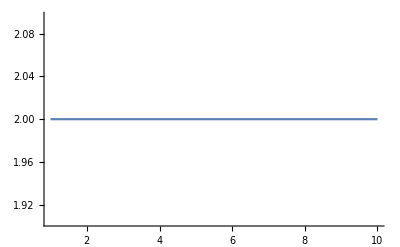

```mathematica
Plot[Abs[(1-ⅇ^((2 ⅈ π)/k))^(1-α-2 ⅈ λ)]/.{k->2,α->0},{λ,1,10}]
```

```mathematica
1
```

```mathematica
Plot[Re[QGamma[3-I z,- E^-0.01]],{z,0,100}]
```

$Aborted

```mathematica
ComplexPlot3D[QGamma[z,ⅈ E^-0.00001],{z,-1-I,1+I},PlotLegends->Automatic]
```

$Aborted

```mathematica
Series[((1-ⅇ^((2 ⅈ π)/k))^(2-α-2 ⅈ λ) (1-ⅇ^((4 ⅈ π)/k)))/((-1+ⅇ^((2 ⅈ π (α+2 ⅈ λ))/k)) (-1+ⅇ^((2 ⅈ π (1+α+2 ⅈ λ))/k))),{λ,Infinity,2}]
```

(ⅇ^(-2 ⅈ Log[1-ⅇ^((2 ⅈ π)/k)] λ-(-2+α) Log[1-ⅇ^((2 ⅈ π)/k)]+O[1/λ]^3))/((-1+ⅇ^(-(4 π λ)/k+(2 ⅈ π α)/k+O[1/λ]^3)) (-1+ⅇ^(-(4 π λ)/k+(2 ⅈ π (1+α))/k+O[1/λ]^3)))-(ⅇ^(-2 ⅈ Log[1-ⅇ^((2 ⅈ π)/k)] λ+((4 ⅈ π)/k-(-2+α) Log[1-ⅇ^((2 ⅈ π)/k)])+O[1/λ]^3))/((-1+ⅇ^(-(4 π λ)/k+(2 ⅈ π α)/k+O[1/λ]^3)) (-1+ⅇ^(-(4 π λ)/k+(2 ⅈ π (1+α))/k+O[1/λ]^3)))

```mathematica
Series[(1-ⅇ^((2 ⅈ π)/k))^(1/2 (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ-1/4 (-2+k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ) (k+M-M1-mM2-2 θinf+2 ⅈ λ+2 σ))) (1-ⅇ^((4 ⅈ π)/k))^(-θinf+1/2 (k+M-M1-mM2+2 ⅈ λ)+σ),{λ,Infinity,0}]
```

ⅇ^(1/2 Log[1-ⅇ^((2 ⅈ π)/k)] λ^2+(-1/2 ⅈ (-3+k+M-M1-mM2-2 θinf+2 σ) Log[1-ⅇ^((2 ⅈ π)/k)]+ⅈ Log[1-ⅇ^((4 ⅈ π)/k)]) λ+(1/2 (k+M-M1-mM2-2 θinf+2 σ-1/4 (-2+k+M-M1-mM2-2 θinf+2 σ) (k+M-M1-mM2-2 θinf+2 σ)) Log[1-ⅇ^((2 ⅈ π)/k)]+(1/2 (k+M-M1-mM2)-θinf+σ) Log[1-ⅇ^((4 ⅈ π)/k)])+O[1/λ]^2)

```mathematica
({θ1+θoo}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

{1/2 (-k-M+M1+mM2+ⅈ ζ-4 ⅈ λ)}

{(-ⅈ) ∞}

```mathematica
1+Sum[2i+1,{i,1,n-1}]
```

n^2

```mathematica
f[3]/.f[x_]->a x +b
```

3 a+b

```mathematica
{f[3]==3, f[4]==4, f[7]==5, f[8]==6}/.f[x_]->a x^4 +b x^3+ c x^2+d
```

{81 a+27 b+9 c+d==3,256 a+64 b+16 c+d==4,2401 a+343 b+49 c+d==5,4096 a+512 b+64 c+d==6}

```mathematica
Reduce[{f[3]==3, f[4]==4, f[7]==5, f[8]==6}/.f[x_]->a x^4 +b x^3+ c x^2+d]
```

d==-18/65&&c==245/312&&b==-9/52&&a==17/1560

```mathematica
Solve[{θ1+θoo==λ,θ1-θoo==θs},{θ1,θoo}]
```

{{θ1→(θs+λ)/2,θoo→1/2 (-θs+λ)}}

```mathematica
t^((σ+n)^2-θ0^2-θt^2+i)/.σ->σ- 1/2
```

t^(i-θ0^2-θt^2+(-1/2+n+σ)^2)

```mathematica
(-1/2+n+σ)^2-(n+σ)^2//Expand
```

1/4-n-σ

```mathematica
Clear[q]
```

```mathematica
nN=2;
mM=1;
Simplify[Coefficient[Coefficient[(Sum[ϵ^(n+1)ξ^(n^2+n+i)t^((σ+n)^2+(1/4+n+σ)-θ0^2-θt^2+i)Subscript[B, i][θt,σ+ 1/2,+n],{n,-1,1},{i,0,2}]/.{θt->θt-1/2,t-> q^-1 t})(Sum[ϵ^(n-1)ξ^(n^2-n+i)t^((σ+n)^2+(1/4-n-σ)-θ0^2-θt^2+i)Subscript[B, i][θt,σ- 1/2+n],{n,-1,1},{i,0,2}]/.{θt->θt+1/2,t-> q t}),ξ,nN],ϵ,mM],{t>0,q>0}]
Simplify[Coefficient[Coefficient[(Sum[ϵ^(n+1)ξ^(n^2+n+i)t^((σ+n)^2+(1/4+n+σ)-θ0^2-θt^2+i)Subscript[B, i][θt,σ+ 1/2,+n],{n,-1,1},{i,0,2}]/.{θt->θt-1/2,t->  t})(Sum[ϵ^(n-1)ξ^(n^2-n+i)t^((σ+n)^2+(1/4-n-σ)-θ0^2-θt^2+i)Subscript[B, i][θt,σ- 1/2+n],{n,-1,1},{i,0,2}]/.{θt->θt+1/2,t-> t}),ξ,nN],ϵ,mM],{t>0,q>0}]
```

q^(-2 (1+θt+2 σ)) t^(-2 (θ0^2+θt^2)+2 (1+σ+σ^2)) (B_0[1/2+θt,-1/2+σ] B_0[-1/2+θt,1/2+σ,1]+q^(4 σ) (q^2 B_1[1/2+θt,1/2+σ] B_1[-1/2+θt,1/2+σ,0]+q^4 B_0[-1/2+θt,1/2+σ,0] B_2[1/2+θt,1/2+σ]+B_0[1/2+θt,1/2+σ] B_2[-1/2+θt,1/2+σ,0]))

t^(2 (1-θ0^2-θt^2+σ+σ^2)) (B_0[1/2+θt,-1/2+σ] B_0[-1/2+θt,1/2+σ,1]+B_1[1/2+θt,1/2+σ] B_1[-1/2+θt,1/2+σ,0]+B_0[-1/2+θt,1/2+σ,0] B_2[1/2+θt,1/2+σ]+B_0[1/2+θt,1/2+σ] B_2[-1/2+θt,1/2+σ,0])

```mathematica
Simplify[Coefficient[Coefficient[(Sum[ϵ^n ξ^(n^2+i)t^((σ+n)^2-θ0^2-θt^2+i)Subscript[B, i][θt,σ+n],{n,-1,1},{i,0,1}]/.{θt->θt-1/2,σ->σ+ 1/2,t->  t})(Sum[ϵ^n ξ^(n^2+i)t^((σ+n)^2-θ0^2-θt^2+i)Subscript[B, i][θt,σ+n],{n,-1,1},{i,0,1}]/.{θt->θt+1/2,σ->σ- 1/2,t-> t}),ξ,1],ϵ,0],{t>0,q>0}]
```

t^(1-2 θ0^2-2 θt^2+2 σ^2) (B_0[1/2+θt,-1/2+σ] B_1[-1/2+θt,1/2+σ]+B_0[-1/2+θt,1/2+σ] B_1[1/2+θt,-1/2+σ])

```mathematica
(1/((1-q)^(-σ^2))/.{σ->σ+1/2})(1/((1-q)^(-σ^2))/.{σ->σ-1/2})//Simplify
```

(1-q)^(1/2+2 σ^2)

```mathematica
({q^(2I λ)}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

{ⅇ^(-(4 π λ)/k)}

{0}

```mathematica
({  }/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

```mathematica
({τ1 τ2- q^(-2θt) τ3 τ4 -(1-q^(-2θt) t)τ7 τ8  }/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

{τ1 τ2-ⅇ^(-(2 ⅈ M π)/k) τ3 τ4-τ7 τ8+ⅇ^(-(2 ⅈ (k+M-M1) π)/k) τ7 τ8}

{τ1 τ2-ⅇ^(-(2 ⅈ M π)/k) τ3 τ4-τ7 τ8+ⅇ^(-(2 ⅈ (k+M-M1) π)/k) τ7 τ8}

```mathematica
(*full eqns*)
```

```mathematica
a
```

{τ1 τ2-τ5 τ6+ⅇ^((2 ⅈ π (k+M-mM2+2 ⅈ λ))/k) (-τ3 τ4+τ5 τ6),dτ5 (-1+ⅇ^(-(2 ⅈ (k+M-M1) π)/k)) uτ6+τ1 τ2-ⅇ^((2 ⅈ M1 π)/k) τ3 τ4,dτ7 (-1+ⅇ^((2 ⅈ π (k+M-mM2+2 ⅈ λ))/k)) uτ8+τ1 τ2-τ3 τ4,τ1 τ2-ⅇ^(-(2 ⅈ M π)/k) τ3 τ4-τ7 τ8+ⅇ^(-(2 ⅈ (k+M-M1) π)/k) τ7 τ8,-dτ1 τ2+dτ5 τ6+dτ7 ⅇ^((ⅈ π (-1+2 k+2 M+M1-mM2-ⅈ ζ+4 ⅈ λ))/k) τ8,-dτ2 τ1+dτ5 τ6+dτ7 ⅇ^((ⅈ π (-1+2 k+2 M+M1-mM2+ⅈ ζ))/k) τ8,dτ3 ⅇ^((ⅈ M π)/k) τ4+dτ5 τ6+dτ7 ⅇ^((π (2 ⅈ M+ζ))/k) τ8,dτ4 ⅇ^((ⅈ M π)/k) τ3+dτ5 τ6+dτ7 ⅇ^((2 ⅈ M π-π ζ)/k) τ8}

{τ1 τ2-τ5 τ6,dτ5 (-1+ⅇ^(-(2 ⅈ (k+M-M1) π)/k)) uτ6+τ1 τ2-ⅇ^((2 ⅈ M1 π)/k) τ3 τ4,-dτ7 uτ8+τ1 τ2-τ3 τ4,τ1 τ2-ⅇ^(-(2 ⅈ M π)/k) τ3 τ4-τ7 τ8+ⅇ^(-(2 ⅈ (k+M-M1) π)/k) τ7 τ8,-dτ1 τ2+dτ5 τ6,-dτ2 τ1+dτ5 τ6+dτ7 ⅇ^((ⅈ π (-1+2 k+2 M+M1-mM2+ⅈ ζ))/k) τ8,dτ3 ⅇ^((ⅈ M π)/k) τ4+dτ5 τ6+dτ7 ⅇ^((π (2 ⅈ M+ζ))/k) τ8,dτ4 ⅇ^((ⅈ M π)/k) τ3+dτ5 τ6+dτ7 ⅇ^((2 ⅈ M π-π ζ)/k) τ8}

```mathematica
({dτ1 τ2-q^(-2θoo)τ1 dτ2- (1-q^(-2θoo))dτ5 τ6,dτ3 τ4-q^(2θ0)τ3 dτ4-q^-θt (1-q^(2θ0))dτ5 τ6,dτ1 τ2-q^(-θ0-θ1-θoo-1/2)t dτ3 τ4 - (1-q^(-θ0-θ1-θoo-1/2)t)dτ5 τ6,q^(-2θ1-2θoo)(τ1 τ2 - τ3 τ4)(τ1 τ2 -q^(2θt) τ3 τ4)-q^(-2θ1-2θoo)(1-q^(2θ1)t^-1)(1-q^(2θt)t^-1)q^(2 θoo)(dτ1 τ2 - dτ5 τ6)(τ1 uτ2 - τ5 uτ6)}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

{-dτ2 ⅇ^((2 π (ζ-2 λ))/k) τ1+dτ1 τ2+dτ5 (-1+ⅇ^((2 π (ζ-2 λ))/k)) τ6,-dτ4 ⅇ^((2 π ζ)/k) τ3+dτ3 τ4-dτ5 ⅇ^(-(ⅈ M π)/k) (-1+ⅇ^((2 π ζ)/k)) τ6,dτ1 τ2-dτ3 ⅇ^((ⅈ π (-1+k+M+M1-mM2+4 ⅈ λ))/k) τ4+dτ5 (-1+ⅇ^((ⅈ π (-1+k+M+M1-mM2+4 ⅈ λ))/k)) τ6,ⅇ^((2 ⅈ π (k+M-M1-mM2-ⅈ ζ+4 ⅈ λ))/k) (τ1 τ2-τ3 τ4) (τ1 τ2-ⅇ^((2 ⅈ M π)/k) τ3 τ4)+ⅇ^(-(2 ⅈ M1 π)/k) (-1+ⅇ^((2 ⅈ (k+M-M1) π)/k)) (-1+ⅇ^((2 ⅈ π (k+M-mM2+2 ⅈ λ))/k)) (uτ2 τ1-uτ6 τ5) (dτ1 τ2-dτ5 τ6)}

{dτ1 τ2-dτ5 τ6,-dτ4 ⅇ^((2 π ζ)/k) τ3+dτ3 τ4-dτ5 ⅇ^(-(ⅈ M π)/k) (-1+ⅇ^((2 π ζ)/k)) τ6,dτ1 τ2-dτ5 τ6,-ⅇ^(-(2 ⅈ M1 π)/k) (-1+ⅇ^((2 ⅈ (k+M-M1) π)/k)) (uτ2 τ1-uτ6 τ5) (dτ1 τ2-dτ5 τ6)}

```mathematica
{dτ1 τ2-dτ5 τ6,-dτ4 ⅇ^((2 π ζ)/k) τ3+dτ3 τ4-dτ5 ⅇ^(-(ⅈ M π)/k) (-1+ⅇ^((2 π ζ)/k)) τ6,dτ1 τ2-dτ5 τ6,-ⅇ^(-(2 ⅈ M1 π)/k) (-1+ⅇ^((2 ⅈ (k+M-M1) π)/k)) (uτ2 τ1-uτ6 τ5) (dτ1 τ2-dτ5 τ6)}/.{mM-> -I x}/.{x->Infinity}
```

{dτ1 τ2-dτ5 τ6,-dτ4 ⅇ^((2 π ζ)/k) τ3+dτ3 τ4-dτ5 ⅇ^(-(ⅈ M π)/k) (-1+ⅇ^((2 π ζ)/k)) τ6,dτ1 τ2-dτ5 τ6,-ⅇ^(-(2 ⅈ M1 π)/k) (-1+ⅇ^((2 ⅈ (k+M-M1) π)/k)) (uτ2 τ1-uτ6 τ5) (dτ1 τ2-dτ5 τ6)}

```mathematica
{dτ1 τ2-dτ5 τ6,-dτ4 ⅇ^((2 π ζ)/k) τ3+dτ3 τ4-dτ5 ⅇ^(-(ⅈ M π)/k) (-1+ⅇ^((2 π ζ)/k)) τ6,dτ1 τ2-dτ5 τ6,-ⅇ^(-(2 ⅈ M1 π)/k) (-1+ⅇ^((2 ⅈ (k+M-M1) π)/k)) (uτ2 τ1-uτ6 τ5) (dτ1 τ2-dτ5 τ6)}/.{M1->mM1-I λ,ζ->-λ}
Limit[%,λ->Infinity]
```

{dτ1 τ2-dτ5 τ6,-dτ4 ⅇ^(-(2 π λ)/k) τ3+dτ3 τ4-dτ5 ⅇ^(-(ⅈ M π)/k) (-1+ⅇ^(-(2 π λ)/k)) τ6,dτ1 τ2-dτ5 τ6,-ⅇ^(-(2 ⅈ π (mM1-ⅈ λ))/k) (-1+ⅇ^((2 ⅈ π (k+M-mM1+ⅈ λ))/k)) (uτ2 τ1-uτ6 τ5) (dτ1 τ2-dτ5 τ6)}

{dτ1 τ2-dτ5 τ6,dτ3 τ4+dτ5 ⅇ^(-(ⅈ M π)/k) τ6,dτ1 τ2-dτ5 τ6,0}

```mathematica
({q^θ0,q^θ1,q^θt,q^(θ1-θoo)}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify
Limit[%,λ->Infinity]
```

{ⅇ^((π ζ)/k),ⅇ^((ⅈ π (-k-M+M1+mM2-2 ⅈ λ))/k),ⅇ^((ⅈ (k+M) π)/k),ⅇ^(-(ⅈ π (k+M-M1-mM2+ⅈ ζ))/k)}

{ⅇ^((π ζ)/k),ComplexInfinity,ⅇ^((ⅈ (k+M) π)/k),ⅇ^(-(ⅈ π (k+M-M1-mM2+ⅈ ζ))/k)}

```mathematica
Series[ⅇ^(-(2 π (ζ-2 λ))/k) (-1+ⅇ^((2 ⅈ (k+M-M1) π)/k)) (-1+ⅇ^(-(2 ⅈ π (k+M-mM2+2 ⅈ λ))/k)),{λ,Infinity,2}]
```

ⅇ^((4 π λ)/k-(2 (π ζ))/k+O[1/λ]^3)-ⅇ^((4 π λ)/k+((2 ⅈ (k+M-M1) π)/k-(2 π ζ)/k)+O[1/λ]^3)+ⅇ^((8 π λ)/k-(2 ⅈ (M1 π-mM2 π-ⅈ π ζ))/k+O[1/λ]^3)-ⅇ^((8 π λ)/k+(-(2 ⅈ (k+M-mM2) π)/k-(2 π ζ)/k)+O[1/λ]^3)

```mathematica
Series[-(ⅈ π (k+M-M1-mM2-ⅈ ζ+4 ⅈ λ))/k,{λ,Infinity,3}]
```

(4 π λ)/k-(ⅈ π (k+M-M1-mM2-ⅈ ζ))/k+O[1/λ]^4

```mathematica
P[M2+1,M]P[M2,M] E^((2π I)/k(-2 I λ))//Simplify
```

ⅇ^((π (16 λ+M (ⅈ+2 ⅈ M2^2+4 λ-16 ⅈ λ^2+M2 (2 ⅈ+8 λ))))/(4 k))

```mathematica
Series[(π (16 λ+M (ⅈ+2 ⅈ M2^2+4 λ-16 ⅈ λ^2+M2 (2 ⅈ+8 λ))))/(4 k),{λ,0,3}]
```

(ⅈ M (1+2 M2+2 M2^2) π)/(4 k)+((4+M+2 M M2) π λ)/k-(4 ⅈ M π λ^2)/k+O[λ]^4

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(qNek[q^(σ  - θt -  θ0),q,q^-1,Y[[1]],{}]qNek[q^(σ  - θt + θ0),q,q^-1,Y[[1]],{}]qNek[q^(- σ  - θt -  θ0),q,q^-1,Y[[2]],{}]qNek[q^(- σ  - θt + θ0),q,q^-1,Y[[2]],{}])/(qNek[1,q,q^-1,Y[[1]],Y[[1]]]qNek[q^(2σ),q,q^-1,Y[[1]],Y[[2]]]qNek[q^(-2σ),q,q^-1,Y[[2]],Y[[1]]]qNek[1,q,q^-1,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
({%,t}/.{t->q^M1}/.{q->E^((2π I)/k),θoo->1/2 (I ζ1-I ζ2),θt->1/2(M+k),θ1->1/2 (M1+M2-M-k),θ0->-1/2(I ζ1+I ζ2)}//PowerExpand)/.{ M2->mM2-I 2λ,ζ1->ζ-λ,ζ2->λ}//Simplify;
Limit[%,λ->Infinity]
%/.{ mM2->-I λ}//Simplify;
Limit[%,λ->Infinity]
%/.{ M1->mM1-I λ,ζ->-λ}//Simplify;
Series[%,{λ,Infinity,0}]
```

(q^(1-θ0-2 θt) (q^θ0-q^(θt+σ)-q^(2 θ0+θt+σ)-q^(θt+3 σ)-q^(2 θ0+θt+3 σ)+q^(θ0+4 σ)+2 q^(θ0+2 (θt+σ))) t)/((-1+q)^2 (-1+q^(2 σ))^2)

{(ⅇ^(-(ⅈ π (-2+2 k+2 M-2 M1-ⅈ ζ))/k) (ⅇ^((π ζ)/k)+2 ⅇ^((π (2 ⅈ k+2 ⅈ M+ζ+4 ⅈ σ))/k)+ⅇ^((π (ζ+8 ⅈ σ))/k)-ⅇ^((ⅈ π (k+M+2 σ))/k)-ⅇ^((ⅈ π (k+M-2 ⅈ ζ+2 σ))/k)-ⅇ^((ⅈ π (k+M+6 σ))/k)-ⅇ^((ⅈ π (k+M-2 ⅈ ζ+6 σ))/k)))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2),ⅇ^((2 ⅈ M1 π)/k)}

{(ⅇ^(-(ⅈ π (-2+2 k+2 M-2 M1-ⅈ ζ))/k) (ⅇ^((π ζ)/k)+2 ⅇ^((π (2 ⅈ k+2 ⅈ M+ζ+4 ⅈ σ))/k)+ⅇ^((π (ζ+8 ⅈ σ))/k)-ⅇ^((ⅈ π (k+M+2 σ))/k)-ⅇ^((ⅈ π (k+M-2 ⅈ ζ+2 σ))/k)-ⅇ^((ⅈ π (k+M+6 σ))/k)-ⅇ^((ⅈ π (k+M-2 ⅈ ζ+6 σ))/k)))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2),ⅇ^((2 ⅈ M1 π)/k)}

{-(ⅇ^((π λ)/k-(ⅈ (-2 π+k π+M π-2 mM1 π-6 π σ))/k+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2)-(ⅇ^((π λ)/k-(ⅈ (-2 π+k π+M π-2 mM1 π-2 π σ))/k+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2)+(ⅇ^((2 π λ)/k-(2 ⅈ (-1+k+M-mM1) π)/k+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2)+(2 ⅇ^((2 π λ)/k+(2 ⅈ (π+mM1 π+2 π σ))/k+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2)+(ⅇ^((2 π λ)/k+(-(2 ⅈ (-1+k+M-mM1) π)/k+(8 ⅈ π σ)/k)+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2)-(ⅇ^((3 π λ)/k-(ⅈ (-2 π+k π+M π-2 mM1 π-6 π σ))/k+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2)-(ⅇ^((3 π λ)/k-(ⅈ (-2 π+k π+M π-2 mM1 π-2 π σ))/k+O[1/λ]^2))/((-1+ⅇ^((2 ⅈ π)/k))^2 (-1+ⅇ^((4 ⅈ π σ)/k))^2),ⅇ^((2 π λ)/k+(2 ⅈ mM1 π)/k+O[1/λ]^2)}

```mathematica
Solve[{-θt-θ0==-I λ, -θt+θ0==-θas},{θ0,θt}]
```

{{θ0→1/2 (-θas+ⅈ λ),θt→1/2 (θas+ⅈ λ)}}

```mathematica
(2 q^(1+2 σ) t)/((-1+q)^2 (-1+q^(2 σ))^2)
```

```mathematica
(-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2))/.{θas->θas,σ->σ,t->t}/.{t-> q^(I λ)t,θas->ⅈ λ}//PowerExpand//Simplify
(%/.λ->-I Log[A]/Log[q]//PowerExpand//Simplify)/.A->0//PowerExpand//Simplify
```

(q (1+q^(4 σ)-q^(ⅈ λ+σ)-q^(ⅈ λ+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)/(-(q^(1+σ) (1+q^(2 σ)))/((-1+q)^2 (-1+q^(2 σ))^2)/.{σ->2σ})//FullSimplify
```

-q^(-2 σ) (1+q^(2 σ))^2 t

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(fMN[q^-σ,q^-1,q,Y[[1]]]fMN[q^σ,q^-1,q,Y[[2]]]qNek[q^(σ  - θas),q^-1,q,Y[[1]],{}]qNek[q^(- σ  - θas),q^-1,q,Y[[2]],{}])/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
```

-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
(q^(2-2 θas) (q^(3+6 σ) (-q^θas+q^σ) (q-q^(2 σ))^2 (-q^θas+q^(1+σ))-q^(2+3 σ) (1+q)^2 (-q^θas+q^σ) (-1+q^(2 σ))^2 (-1+q^(θas+σ))+(q-q^(2 σ))^2 (-1+q^(θas+σ)) (-1+q^(1+θas+σ))+q^(6 σ) (-q^θas+q^σ) (-q^(1+θas)+q^σ) (-1+q^(1+2 σ))^2+q^3 (-1+q^(θas+σ)) (-q+q^(θas+σ)) (-1+q^(1+2 σ))^2) t^2)/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)/.{t-> q^(I λ)t,θas->ⅈ λ}//PowerExpand//Simplify
(%/.λ->-I Log[A]/Log[q]//PowerExpand//Simplify)/.A->0//PowerExpand//Simplify
```

(q^2 (q^(3+6 σ) (-q^(ⅈ λ)+q^σ) (q-q^(2 σ))^2 (-q^(ⅈ λ)+q^(1+σ))-q^(2+3 σ) (1+q)^2 (-q^(ⅈ λ)+q^σ) (-1+q^(2 σ))^2 (-1+q^(ⅈ λ+σ))+(q-q^(2 σ))^2 (-1+q^(ⅈ λ+σ)) (-1+q^(1+ⅈ λ+σ))+q^(6 σ) (-q^(1+ⅈ λ)+q^σ) (-q^(ⅈ λ)+q^σ) (-1+q^(1+2 σ))^2+q^3 (-1+q^(ⅈ λ+σ)) (-q+q^(ⅈ λ+σ)) (-1+q^(1+2 σ))^2) t^2)/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)

(q^2 ((q-q^(2 σ))^2+q^(4+8 σ) (q-q^(2 σ))^2+q^(2+4 σ) (1+q)^2 (-1+q^(2 σ))^2+q^4 (-1+q^(1+2 σ))^2+q^(8 σ) (-1+q^(1+2 σ))^2) t^2)/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)

```mathematica
Series[{(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2),(2 q^(1+2 σ) t)/((-1+q)^2 (-1+q^(2 σ))^2)}/.{q->E^R,t->R^4 t},{R,0,0}]
```

{t/(2 σ^2)+O[R]^1,t/(2 σ^2)+O[R]^1}

```mathematica
(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)/((2 q^(1+2 σ) t)/((-1+q)^2 (-1+q^(2 σ))^2))//Simplify
```

1/2 q^(-2 σ) (1+q^(4 σ))

```mathematica
(q^2 ((q-q^(2 σ))^2+q^(4+8 σ) (q-q^(2 σ))^2+q^(2+4 σ) (1+q)^2 (-1+q^(2 σ))^2+q^4 (-1+q^(1+2 σ))^2+q^(8 σ) (-1+q^(1+2 σ))^2) t^2)/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)/((q^(4+4 σ) (3+2 q+3 q^2-2 q^(2 σ)+3 q^(4 σ)-12 q^(1+2 σ)-2 q^(2+2 σ)+2 q^(1+4 σ)+3 q^(2+4 σ)) t^2)/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2))//Together
```

(q^(-2-4 σ) (q^2+q^4+q^(4 σ)+q^(8 σ)-2 q^(1+2 σ)-2 q^(5+2 σ)+q^(2+4 σ)+2 q^(3+4 σ)+q^(4+4 σ)+q^(6+4 σ)-2 q^(2+6 σ)-4 q^(3+6 σ)-2 q^(4+6 σ)+q^(2+8 σ)+2 q^(3+8 σ)+q^(4+8 σ)+q^(6+8 σ)-2 q^(1+10 σ)-2 q^(5+10 σ)+q^(2+12 σ)+q^(4+12 σ)))/(3+2 q+3 q^2-2 q^(2 σ)+3 q^(4 σ)-12 q^(1+2 σ)-2 q^(2+2 σ)+2 q^(1+4 σ)+3 q^(2+4 σ))

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(1)/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
```

(2 q^(1+2 σ) t)/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(fMN[q^-σ,q^-1,q,Y[[1]]]fMN[q^σ,q^-1,q,Y[[2]]]fMN[q^-σ,q^-1,q,Y[[1]]]fMN[q^σ,q^-1,q,Y[[2]]])/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
```

(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
θt-θ0/.{t-> q^(I λ)t,θ0->1/2 (-θas+ⅈ λ),θt->1/2 (θas+ⅈ λ)}//Simplify
```

θas

```mathematica
Solve[{θt-θ0==θas,θt+θ0==θas+I λ},{θ0,θt}]
```

{{θ0→(ⅈ λ)/2,θt→1/2 (2 θas+ⅈ λ)}}

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(qNek[q^(σ  - θt -  θ0),q^-1,q,Y[[1]],{}]qNek[q^(- σ  - θt -  θ0),q^-1,q,Y[[2]],{}]qNek[q^(σ  - θt + θ0),q^-1,q,Y[[1]],{}]qNek[q^(- σ  - θt +  θ0),q,q^-1,Y[[2]],{}])/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
%/.{t-> q^(I λ)t,θ0->(ⅈ λ)/2,θt->1/2 (2 θas+ⅈ λ)}//PowerExpand//Simplify
(%/.λ->-I Log[A]/Log[q]//PowerExpand//Simplify)/.A->0//Simplify
```

(q^(1-θ0-2 θt) (q^θ0-q^(θt+σ)-q^(2 θ0+θt+σ)-q^(θt+3 σ)-q^(2 θ0+θt+3 σ)+q^(θ0+4 σ)+2 q^(θ0+2 (θt+σ))) t)/((-1+q)^2 (-1+q^(2 σ))^2)

(q^(1-2 θas) (1+q^(4 σ)-q^(θas+σ)-q^(θas+ⅈ λ+σ)+2 q^(2 θas+ⅈ λ+2 σ)-q^(θas+3 σ)-q^(θas+ⅈ λ+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

-(q^(1-2 θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
(q^(3/2-2 θas) (1-q^(θas+σ)-q^(1+θas+3 σ)+q^(2+4 σ)) t)/((-1+q)^2 (-1+q^(1+2 σ))^2)/(-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2))//FullSimplify
```

```mathematica
-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)+0) t)/((-1+q)^2 (-1+q^(2 σ))^2)/(-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2))//FullSimplify
```

1

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
Sum[
(fMN[q^-σ,q^-1,q,Y[[1]]]fMN[q^σ,q^-1,q,Y[[2]]])^2/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
```

(q (1+q^(4 σ)))/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
((fMN[q^-σ,q^-1,q,Y[[1]]]fMN[q^σ,q^-1,q,Y[[2]]])^1 qNek[q^(σ  - θas),q^-1,q,Y[[1]],{}]qNek[q^(- σ  - θas),q^-1,q,Y[[2]],{}])/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
%/.{θas->θas-1/2,σ->σ,t->q^(-1/2)t}//PowerExpand
%/.{t-> q^(I λ/2) q^(-M/2 0)t,θas->0 M/2+(ⅈ λ)/2}//PowerExpand//Simplify
%/.λ->-2I Log[A]/Log[q]
((%/.λ->-I Log[A]/(2Log[q])//PowerExpand//Simplify)//Factor)/.A->0//Simplify
```

-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

-(q^(1-θas) (-1-q^(4 σ)+q^(-1/2+θas+σ)+q^(-1/2+θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

-(q (-1-q^(4 σ)+q^(-1/2+(ⅈ λ)/2+σ)+q^(1/2 (-1+ⅈ λ+6 σ))) t)/((-1+q)^2 (-1+q^(2 σ))^2)

-(q (-1+A q^(-1/2+σ)-q^(4 σ)+q^(1/2 (-1+6 σ+(2 Log[A])/Log[q]))) t)/((-1+q)^2 (-1+q^(2 σ))^2)

(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

```mathematica
(q (1+q^(4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)/((q (1+q^(4 σ)))/((-1+q)^2 (-1+q^(2 σ))^2) t/.{σ->σ})//Simplify
```

1

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(qNek[q^(σ  - θt -  θ0),q^-1,q,Y[[1]],{}]qNek[q^(- σ  - θt -  θ0),q^-1,q,Y[[2]],{}]qNek[q^(σ  - θt + θ0),q^-1,q,Y[[1]],{}]qNek[q^(- σ  - θt +  θ0),q,q^-1,Y[[2]],{}])/(qNek[1,q^-1,q,Y[[1]],Y[[1]]]qNek[q^(2σ),q^-1,q,Y[[1]],Y[[2]]]qNek[q^(-2σ),q^-1,q,Y[[2]],Y[[1]]]qNek[1,q^-1,q,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
%/.{θt->θt+1/2}/.{t-> q^(I λ)t,θ0->(1/2) (-θas+ⅈ λ),θt->(1/2) (θas+ⅈ λ)}//PowerExpand//Simplify
((%/.λ->-I Log[A]/Log[q]//PowerExpand)/.{A->0}//Simplify)/(-((q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2))/.{θas->θas+1/2})//FullSimplify
```

(q^(1-θ0-2 θt) (q^θ0-q^(θt+σ)-q^(2 θ0+θt+σ)-q^(θt+3 σ)-q^(2 θ0+θt+3 σ)+q^(θ0+4 σ)+2 q^(θ0+2 (θt+σ))) t)/((-1+q)^2 (-1+q^(2 σ))^2)

-(q^-θas (-1-q^(4 σ)+q^(1/2+θas+σ)+q^(1/2+ⅈ λ+σ)-2 q^(1+θas+ⅈ λ+2 σ)+q^(1/2+θas+3 σ)+q^(1/2+ⅈ λ+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

1/(√q)

```mathematica
(q^(1/2-θas) (√q-q^(θas+σ)-q^(θas+3 σ)+q^(1/2+4 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)/(-(q^(1-θas) (-1-q^(4 σ)+q^(θas+σ)+q^(θas+3 σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)/.{θas->θas-1/2})//Simplify
```

1/(√q)

```mathematica
(t (-θ0^2+θt^2+σ^2))/(2 σ^2)/.{θ0->1/2 (θas+I λ),θt->1/2 (-θas+I λ),t->t/λ}//Simplify
```

1/2 t (1/λ-(ⅈ θas)/σ^2)

```mathematica
Series[(q^(1-θ0-2 θt) (q^θ0-q^(θt+σ)-q^(2 θ0+θt+σ)-q^(θt+3 σ)-q^(2 θ0+θt+3 σ)+q^(θ0+4 σ)+2 q^(θ0+2 (θt+σ))) t)/((-1+q)^2 (-1+q^(2 σ))^2)/.{q->E^R,t->R t},{R,0,-1}]
```

(t (-θ0^2+θt^2+σ^2))/(2 σ^2 R)+O[R]^0

```mathematica
q^(ϵ σ  - θt - ϵ' θ0)
```

```mathematica
instno=2;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(qNek[q^(σ  - θt -  θ0),q,q^-1,Y[[1]],{}]qNek[q^(σ  - θt + θ0),q,q^-1,Y[[1]],{}]qNek[q^(- σ  - θt -  θ0),q,q^-1,Y[[2]],{}]qNek[q^(- σ  - θt + θ0),q,q^-1,Y[[2]],{}])/(qNek[1,q,q^-1,Y[[1]],Y[[1]]]qNek[q^(2σ),q,q^-1,Y[[1]],Y[[2]]]qNek[q^(-2σ),q,q^-1,Y[[2]],Y[[1]]]qNek[1,q,q^-1,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
Series[%/.{q->E^R,t-> R^2 t},{R,0,0}]//Normal//FullSimplify
```

(q^(2-2 θ0-4 θt) (q^(2+4 σ) (-q^(θ0+θt)+q^σ) (q-q^(2 σ))^2 (-q^(θ0+θt)+q^(1+σ)) (-q^θt+q^(θ0+σ)) (-q^θt+q^(1+θ0+σ))+q^(2+2 σ) (1+q)^2 (-q^(θ0+θt)+q^σ) (-1+q^(2 σ))^2 (-q^θt+q^(θ0+σ)) (-q^θ0+q^(θt+σ)) (-1+q^(θ0+θt+σ))+(q-q^(2 σ))^2 (q^θ0-q^(θt+σ)) (q^θ0-q^(1+θt+σ)) (-1+q^(θ0+θt+σ)) (-1+q^(1+θ0+θt+σ))+q^(4 σ) (-q^(θ0+θt)+q^σ) (-q^(1+θ0+θt)+q^σ) (-q^θt+q^(θ0+σ)) (-q^(1+θt)+q^(θ0+σ)) (-1+q^(1+2 σ))^2+q^2 (q^θ0-q^(θt+σ)) (q^(1+θ0)-q^(θt+σ)) (-1+q^(θ0+θt+σ)) (-q+q^(θ0+θt+σ)) (-1+q^(1+2 σ))^2) t^2)/((-1+q)^4 (1+q)^2 (q-q^(2 σ))^2 (-1+q^(2 σ))^2 (-1+q^(1+2 σ))^2)

(t^2 (θt^2+θt^4+(1-14 θt^2+8 θt^4) σ^2+(-3+16 θt^2) σ^4+8 σ^6+θ0^4 (1+8 σ^2)-θ0^2 (1-2 σ^2+16 σ^4+2 θt^2 (1+8 σ^2))))/(4 (σ-4 σ^3)^2)

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
t^instno Sum[
(qNek[q^(σ  - θas),q,q^-1,{},Y[[1]]]qNek[q^(-σ  - θas),q,q^-1,{},Y[[2]]])/(qNek[1,q,q^-1,Y[[1]],Y[[1]]]qNek[q^(2σ),q,q^-1,Y[[1]],Y[[2]]]qNek[q^(-2σ),q,q^-1,Y[[2]],Y[[1]]]qNek[1,q,q^-1,Y[[2]],Y[[2]]])//Simplify,{Y,tableaux}]/.{q1->q^1,q2->q^-1}//Simplify
Series[%/.{q->E^R,t-> R^3 t},{R,0,0}]//Normal//FullSimplify
```

-(q^(1-θ+σ) (1+q^(2 σ)-2 q^(θ+σ)) t)/((-1+q)^2 (-1+q^(2 σ))^2)

(t θ)/(2 σ^2)

```mathematica
Nf=2;
Table[
instno=k;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
Sum[Product[Product[ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[ϕ[-σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}],{i,1,Nf}]/Zbifund[σ1,-σ1,Y[[1]],Y[[2]],σ1,-σ1,Y[[1]],Y[[2]],0]//Cancel,{Y,tableaux}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}/.{m1->θ0+θt,m2->-θ0+θt,σ1->σ}//FullSimplify,{k,0,2}]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

{1,(-θ0^2+θt^2+σ^2)/(2 σ^2),(θt^2+θt^4+(1-14 θt^2+8 θt^4) σ^2+(-3+16 θt^2) σ^4+8 σ^6+θ0^4 (1+8 σ^2)-θ0^2 (1-2 σ^2+16 σ^4+2 θt^2 (1+8 σ^2)))/(4 (σ-4 σ^3)^2)}

```mathematica
Nf=1;
Table[
instno=k;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
Sum[Product[Product[ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[ϕ[-σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}],{i,1,Nf}]/Zbifund[σ1,-σ1,Y[[1]],Y[[2]],σ1,-σ1,Y[[1]],Y[[2]],0]//Cancel,{Y,tableaux}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}/.{σ1->σ}//FullSimplify,{k,0,3}]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

{1,m1/(2 σ^2),(m1^2+(-3+8 m1^2) σ^2)/(4 (σ-4 σ^3)^2),(m1 (-1+4 σ^2-9 σ^4+m1^2 (3-5 σ^2+8 σ^4)))/(24 (σ-5 σ^3+4 σ^5)^2)}

```mathematica
Solve[{-θ0+θt==-λ,-θ0-θt==m},{θ0,θt}]
```

{{θ0→1/2 (-m+λ),θt→1/2 (-m-λ)}}

```mathematica
Series[1+t(-θ0^2+θt^2+σ^2)/(2 σ^2)+t^2(θt^2+θt^4+(1-14 θt^2+8 θt^4) σ^2+(-3+16 θt^2) σ^4+8 σ^6+θ0^4 (1+8 σ^2)-θ0^2 (1-2 σ^2+16 σ^4+2 θt^2 (1+8 σ^2)))/(4 (σ-4 σ^3)^2)/.{t-> λ^2 t,θ0->+λ^1,θt-> m^(1/2),σ-> σ},{λ,Infinity,2}]//Simplify
```

(t^2 (1+8 σ^2) λ^8)/(4 (σ-4 σ^3)^2)+(t^2 (-1+2 σ^2-16 σ^4-2 m (1+8 σ^2)) λ^6)/(4 (σ-4 σ^3)^2)+1/4 t (-2/σ^2+(t (m+m^2+(1-14 m+8 m^2) σ^2+(-3+16 m) σ^4+8 σ^6))/((σ-4 σ^3)^2)) λ^4+(t (m+σ^2) λ^2)/(2 σ^2)+1+O[1/λ]^3

```mathematica
Coefficient[q^(1-θ0-2 θt) (q^θ0-q^(θt+σ)-q^(2 θ0+θt+σ)-q^(θt+3 σ)-q^(2 θ0+θt+3 σ)+q^(θ0+4 σ)+2 q^(θ0+2 (θt+σ))) t/.{θ0->Log[λ]/Log[q]},λ,0]//Simplify
Series[(q^(2-2 θ0-4 θt) (q^(2+4 σ) (-q^(θ0+θt)+q^σ) (q-q^(2 σ))^2 (-q^(θ0+θt)+q^(1+σ)) (-q^θt+q^(θ0+σ)) (-q^θt+q^(1+θ0+σ))+q^(2+2 σ) (1+q)^2 (-q^(θ0+θt)+q^σ) (-1+q^(2 σ))^2 (-q^θt+q^(θ0+σ)) (-q^θ0+q^(θt+σ)) (-1+q^(θ0+θt+σ))+(q-q^(2 σ))^2 (q^θ0-q^(θt+σ)) (q^θ0-q^(1+θt+σ)) (-1+q^(θ0+θt+σ)) (-1+q^(1+θ0+θt+σ))+q^(4 σ) (-q^(θ0+θt)+q^σ) (-q^(1+θ0+θt)+q^σ) (-q^θt+q^(θ0+σ)) (-q^(1+θt)+q^(θ0+σ)) (-1+q^(1+2 σ))^2+q^2 (q^θ0-q^(θt+σ)) (q^(1+θ0)-q^(θt+σ)) (-1+q^(θ0+θt+σ)) (-q+q^(θ0+θt+σ)) (-1+q^(1+2 σ))^2) t^2)/.{θ0->Log[λ]/Log[q]},{λ,0,0}]//Factor
```

q^(1-2 θt) (1+q^(4 σ)+2 q^(2 (θt+σ))) t

1/λ^2 q^(2-4 θt) (q^(1+2 θt+2 σ) (q-q^(2 σ))^2+q^(3+2 θt+6 σ) (q-q^(2 σ))^2+q^(2+2 θt+4 σ) (1+q)^2 (-1+q^(2 σ))^2+q^(3+2 θt+2 σ) (-1+q^(1+2 σ))^2+q^(1+2 θt+6 σ) (-1+q^(1+2 σ))^2) t^2+1/λ q^(2-4 θt) (-q^(2+θt+3 σ) (1+q)^2 (1+q^(2 θt)) (-1+q^(2 σ))^2 (1+q^(2 σ))-q^(θt+5 σ) (-1+q^(1+2 σ))^2 (q^(1+2 θt)+q^(2+2 θt)+q^(2 σ)+q^(1+2 σ))-q^(2+θt+5 σ) (-q+q^(2 σ))^2 (q^(2 θt)+q^(1+2 θt)+q^(1+2 σ)+q^(2+2 σ))-q^(2+θt+σ) (-1+q^(1+2 σ))^2 (q+q^2+q^(2 θt+2 σ)+q^(1+2 θt+2 σ))-q^(θt+σ) (-q+q^(2 σ))^2 (1+q+q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ))) t^2+q^(2-4 θt) (q^(4 σ) (-1+q^(1+2 σ))^2 (q^(2+4 θt)+q^(4 σ)+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ))+q^(2+4 σ) (-q+q^(2 σ))^2 (q^(4 θt)+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ)+q^(2+4 σ))+q^(2+2 σ) (1+q)^2 (-1+q^(2 σ))^2 (q^(2 θt)+q^(2 σ)+2 q^(2 θt+2 σ)+q^(4 θt+2 σ)+q^(2 θt+4 σ))+q^2 (-1+q^(1+2 σ))^2 (q^2+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ)+q^(4 θt+4 σ))+(-q+q^(2 σ))^2 (1+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ)+q^(2+4 θt+4 σ))) t^2+O[λ]^1

```mathematica
q^(2-4 θt) (q^(4 σ) (-1+q^(1+2 σ))^2 (q^(2+4 θt)+q^(4 σ)+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ))+q^(2+4 σ) (-q+q^(2 σ))^2 (q^(4 θt)+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ)+q^(2+4 σ))+q^(2+2 σ) (1+q)^2 (-1+q^(2 σ))^2 (q^(2 θt)+q^(2 σ)+2 q^(2 θt+2 σ)+q^(4 θt+2 σ)+q^(2 θt+4 σ))+q^2 (-1+q^(1+2 σ))^2 (q^2+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ)+q^(4 θt+4 σ))+(-q+q^(2 σ))^2 (1+q^(2 θt+2 σ)+2 q^(1+2 θt+2 σ)+q^(2+2 θt+2 σ)+q^(2+4 θt+4 σ))) t^2//Factor
```

q^(2-4 θt) (q^2+q^4+q^(4 σ)+q^(8 σ)-2 q^(1+2 σ)-2 q^(5+2 σ)+3 q^(2+2 θt+2 σ)+6 q^(3+2 θt+2 σ)+3 q^(4+2 θt+2 σ)+q^(2+4 σ)+2 q^(3+4 σ)+q^(4+4 σ)+q^(6+4 σ)-2 q^(1+2 θt+4 σ)-4 q^(2+2 θt+4 σ)-4 q^(3+2 θt+4 σ)-4 q^(4+2 θt+4 σ)-2 q^(5+2 θt+4 σ)+3 q^(2+4 θt+4 σ)+2 q^(3+4 θt+4 σ)+3 q^(4+4 θt+4 σ)-2 q^(2+6 σ)-4 q^(3+6 σ)-2 q^(4+6 σ)+2 q^(2 θt+6 σ)+4 q^(1+2 θt+6 σ)-4 q^(3+2 θt+6 σ)+4 q^(5+2 θt+6 σ)+2 q^(6+2 θt+6 σ)-2 q^(2+4 θt+6 σ)-12 q^(3+4 θt+6 σ)-2 q^(4+4 θt+6 σ)+q^(2+8 σ)+2 q^(3+8 σ)+q^(4+8 σ)+q^(6+8 σ)-2 q^(1+2 θt+8 σ)-4 q^(2+2 θt+8 σ)-4 q^(3+2 θt+8 σ)-4 q^(4+2 θt+8 σ)-2 q^(5+2 θt+8 σ)+3 q^(2+4 θt+8 σ)+2 q^(3+4 θt+8 σ)+3 q^(4+4 θt+8 σ)-2 q^(1+10 σ)-2 q^(5+10 σ)+3 q^(2+2 θt+10 σ)+6 q^(3+2 θt+10 σ)+3 q^(4+2 θt+10 σ)+q^(2+12 σ)+q^(4+12 σ)) t^2

```mathematica
-q^(1-θ+σ) (1+q^(2 σ)-2 q^(θ+σ)) t
q^(3-2 θ+2 σ) (q^(1+2 σ) (-q^θ+q^σ) (q-q^(2 σ))^2 (-q^θ+q^(1+σ))-q^(1+σ) (1+q)^2 (-q^θ+q^σ) (-1+q^(2 σ))^2 (-1+q^(θ+σ))+(q-q^(2 σ))^2 (-1+q^(θ+σ)) (-1+q^(1+θ+σ))+q^(2 σ) (-q^θ+q^σ) (-q^(1+θ)+q^σ) (-1+q^(1+2 σ))^2+q (-1+q^(θ+σ)) (-q+q^(θ+σ)) (-1+q^(1+2 σ))^2) t^2//Factor
```

-q^(1-θ+σ) (1+q^(2 σ)-2 q^(θ+σ)) t

q^(3-2 θ+2 σ) (2 q^2+2 q^(4 σ)-2 q^(1+θ+σ)-4 q^(2+θ+σ)-2 q^(3+θ+σ)-q^(1+2 σ)+2 q^(2+2 σ)-q^(3+2 σ)+3 q^(1+2 θ+2 σ)+2 q^(2+2 θ+2 σ)+3 q^(3+2 θ+2 σ)-q^(θ+3 σ)+2 q^(1+θ+3 σ)+6 q^(2+θ+3 σ)+2 q^(3+θ+3 σ)-q^(4+θ+3 σ)-2 q^(1+4 σ)-4 q^(2+4 σ)-2 q^(3+4 σ)+2 q^(4+4 σ)-2 q^(1+2 θ+4 σ)-12 q^(2+2 θ+4 σ)-2 q^(3+2 θ+4 σ)-q^(θ+5 σ)+2 q^(1+θ+5 σ)+6 q^(2+θ+5 σ)+2 q^(3+θ+5 σ)-q^(4+θ+5 σ)-q^(1+6 σ)+2 q^(2+6 σ)-q^(3+6 σ)+3 q^(1+2 θ+6 σ)+2 q^(2+2 θ+6 σ)+3 q^(3+2 θ+6 σ)-2 q^(1+θ+7 σ)-4 q^(2+θ+7 σ)-2 q^(3+θ+7 σ)+2 q^(2+8 σ)) t^2

```mathematica
1/4({{-2, 0, 2, 0, 0}, {-1, -1, 0, 2, 0}, {1, 1, 0, 2, 0}, {0, -2, 2, 0, 0}, {0, 0, 0, 4, -4}}).({{-1/2, -1/2, 1, 0, -1}, {-1/2, -1/2, 1, 0, 1}, {-1/2, -1/2, 1, 1, 0}, {1/2, -1/2, 0, 0, 0}, {-1/2, -1/2, 0, 0, 0}}).{M1,mM2-I 2λ,M+k,-I (ζ-λ),-I λ}//Simplify
```

{-(ⅈ ζ)/2,1/2 (-k-M+M1),1/2 (k+M-mM2+2 ⅈ λ),-1/2 ⅈ (ζ-2 λ),M1}

```mathematica
(*old matrix*)
```

```mathematica
Do[temp=(1/4({{-2, 0, 2, 0, 0}, {-1, -1, 0, 2, 4}, {1, 1, 0, 2, -4}, {0, -2, 2, 0, 0}, {0, 0, 0, 4, -4}}).mat.{M1,mM2-I 2λ,M+k,-I (ζ-λ),-I λ}//Expand);
coefvec = Coefficient[temp,λ,1];
If[coefvec[[1]]==0&&coefvec[[3]]==0&&coefvec[[5]]==0&&Coefficient[temp[[5]],λ,0]==M1,Print[temp],Nothing];
,{mat,matrices}]
```

{-(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,(ⅈ ζ)/2-ⅈ λ,M1}

{-(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,-(ⅈ ζ)/2+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4-(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,k/2+M/2-M1/4-mM2/4-(ⅈ ζ)/2+ⅈ λ,M1}

{(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,(ⅈ ζ)/2-ⅈ λ,M1}

{(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,-(ⅈ ζ)/2+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,k/2+M/2-M1/4-mM2/4+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4-(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,-k/2-M/2+M1/4+mM2/4+(ⅈ ζ)/2-ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4+(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,k/2+M/2-M1/4-mM2/4-(ⅈ ζ)/2+ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,k/2+M/2-M1/4-mM2/4+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,-k/2-M/2+M1/4+mM2/4-ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4+(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,-k/2-M/2+M1/4+mM2/4+(ⅈ ζ)/2-ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,-k/2-M/2+M1/4+mM2/4-ⅈ λ,M1}

```mathematica
Do[temp=(1/4({{-2, 0, 2, 0, 0}, {-1, -1, 0, 2, 4}, {1, 1, 0, 2, -4}, {0, -2, 2, 0, 0}, {0, 0, 0, 4, -4}}).mat.{M1,mM2-I 2λ,M+k,-I (ζ-λ),-I λ}//Expand);
coefvec = Coefficient[temp,λ,1];
If[coefvec[[1]]==0&&coefvec[[3]]==0&&coefvec[[5]]==0&&Coefficient[temp[[5]],λ,0]==M1,Print[temp],Nothing];
,{mat,matrices}]
```

{-(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,(ⅈ ζ)/2-ⅈ λ,M1}

{-(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,-(ⅈ ζ)/2+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4-(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,k/2+M/2-M1/4-mM2/4-(ⅈ ζ)/2+ⅈ λ,M1}

{(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,(ⅈ ζ)/2-ⅈ λ,M1}

{(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,-(ⅈ ζ)/2+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,k/2+M/2-M1/4-mM2/4+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4-(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,-k/2-M/2+M1/4+mM2/4+(ⅈ ζ)/2-ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4+(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,k/2+M/2-M1/4-mM2/4-(ⅈ ζ)/2+ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,k/2+M/2-M1/4-mM2/4+ⅈ λ,M1}

{-k/2-M/2+M1/4+mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,-k/2-M/2+M1/4+mM2/4-ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4+(ⅈ ζ)/2,-M1/4-(3 mM2)/4+ⅈ λ,(3 M1)/4+mM2/4,-k/2-M/2+M1/4+mM2/4+(ⅈ ζ)/2-ⅈ λ,M1}

{k/2+M/2-M1/4-mM2/4,-M1/4-(3 mM2)/4+(ⅈ ζ)/2+ⅈ λ,(3 M1)/4+mM2/4-(ⅈ ζ)/2,-k/2-M/2+M1/4+mM2/4-ⅈ λ,M1}

```mathematica
{(ⅈ ζ)/2,-k/2-M/2+M1/2-mM2/2+ⅈ λ,k/2+M/2-M1,(ⅈ ζ)/2-ⅈ λ,-M1}
```

```mathematica
{-(ⅈ ζ)/2,-k/2-M/2-mM2/2+ⅈ λ,k/2+M/2+M1/2,-(ⅈ ζ)/2+ⅈ λ,M1}
```

```mathematica
{t,q^(-θt-θ0),q^(-θt+θ0),q^(θ1-θinf),q^(θ1+θinf)}/.{q->E^((2π I)/k),θ0->(ⅈ ζ)/2,θ1->-k/2-M/2+M1/2-mM2/2+ⅈ λ,θt->k/2+M/2-M1,θinf->(ⅈ ζ)/2-ⅈ λ,t->q^-M1}//PowerExpand
Limit[%,λ->Infinity]
%/.{ mM2->-I λ}//Simplify;
Limit[%,λ->Infinity]
%/.{M1->-M1,M->M}
%/.{M1->mM1-I λ,ζ->-λ}//Simplify
Limit[%,λ->Infinity]
```

{q^-M1,ⅇ^((2 ⅈ π (-k/2-M/2+M1-(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2+M1+(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2+M1/2-mM2/2-(ⅈ ζ)/2+2 ⅈ λ))/k),ⅇ^((2 ⅈ π (-k/2-M/2+M1/2-mM2/2+(ⅈ ζ)/2))/k)}

{q^-M1,ⅇ^(-(ⅈ π (k+M-2 M1+ⅈ ζ))/k),ⅇ^(-(ⅈ π (k+M-2 M1-ⅈ ζ))/k),0,ⅇ^(-(ⅈ π (k+M-M1+mM2-ⅈ ζ))/k)}

{q^-M1,ⅇ^(-(ⅈ π (k+M-2 M1+ⅈ ζ))/k),ⅇ^(-(ⅈ π (k+M-2 M1-ⅈ ζ))/k),0,0}

{q^M1,ⅇ^(-(ⅈ π (k+M+2 M1+ⅈ ζ))/k),ⅇ^(-(ⅈ π (k+M+2 M1-ⅈ ζ))/k),0,0}

{q^(mM1-ⅈ λ),ⅇ^(-(ⅈ π (k+M+2 mM1-3 ⅈ λ))/k),ⅇ^(-(ⅈ π (k+M+2 mM1-ⅈ λ))/k),0,0}

lim_(λ→∞) {q^(mM1-ⅈ λ),ⅇ^(-(ⅈ π (k+M+2 mM1-3 ⅈ λ))/k),ⅇ^(-(ⅈ π (k+M+2 mM1-ⅈ λ))/k),0,0}

```mathematica
{t,q^(-θt-θ0),q^(-θt+θ0),q^(θ1-θinf),q^(θ1+θinf)}/.{q->E^((2π I)/k),θ0->-(ⅈ ζ)/2,θ1->-k/2-M/2-mM2/2+ⅈ λ,θt->k/2+M/2+M1/2,θinf->-(ⅈ ζ)/2+ⅈ λ,t->q^M1}//PowerExpand
Limit[%,λ->Infinity]
%/.{ mM2->-I λ}//Simplify;
Limit[%,λ->Infinity]
%/.{M1->-M1,M->M}
%/.{M1->mM1-I λ,ζ->-λ}
Limit[%,λ->Infinity]
```

{q^M1,ⅇ^((2 ⅈ π (-k/2-M/2-M1/2+(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2-M1/2-(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2-mM2/2+(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2-mM2/2-(ⅈ ζ)/2+2 ⅈ λ))/k)}

{q^M1,ⅇ^((2 ⅈ π (-k/2-M/2-M1/2+(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2-M1/2-(ⅈ ζ)/2))/k),ⅇ^((2 ⅈ π (-k/2-M/2-mM2/2+(ⅈ ζ)/2))/k),0}

{q^M1,ⅇ^(-(ⅈ π (k+M+M1-ⅈ ζ))/k),ⅇ^(-(ⅈ π (k+M+M1+ⅈ ζ))/k),0,0}

{q^-M1,ⅇ^(-(ⅈ π (k+M-M1-ⅈ ζ))/k),ⅇ^(-(ⅈ π (k+M-M1+ⅈ ζ))/k),0,0}

{q^(-mM1+ⅈ λ),ⅇ^(-(ⅈ π (k+M-mM1+2 ⅈ λ))/k),ⅇ^(-(ⅈ (k+M-mM1) π)/k),0,0}

lim_(λ→∞) {q^(-mM1+ⅈ λ),ⅇ^(-(ⅈ π (k+M-mM1+2 ⅈ λ))/k),ⅇ^(-(ⅈ (k+M-mM1) π)/k),0,0}

```mathematica
q^(-mM1+ⅈ λ)ⅇ^(-(ⅈ π (k+M-mM1+2 ⅈ λ))/k)/.q->E^((2π I)/k)//PowerExpand
Limit[%,λ->Infinity]
```

ⅇ^((2 ⅈ π (-mM1+ⅈ λ))/k-(ⅈ π (k+M-mM1+2 ⅈ λ))/k)

ⅇ^(-(ⅈ (k+M+mM1) π)/k)

```mathematica
(*t, q^(-θt+θ0), product*)
{ⅇ^(-(ⅈ (k+M+mM1) π)/k),ⅇ^(-(ⅈ (k+M-mM1) π)/k),ⅇ^(-(ⅈ (k+M+mM1) π)/k)ⅇ^(-(ⅈ (k+M-mM1) π)/k)}/.{mM1->-I λ}
Limit[%,λ->Infinity]
```

{ⅇ^(-(ⅈ π (k+M-ⅈ λ))/k),ⅇ^(-(ⅈ π (k+M+ⅈ λ))/k),ⅇ^(-(ⅈ π (k+M-ⅈ λ))/k-(ⅈ π (k+M+ⅈ λ))/k)}

{0,ComplexInfinity,ⅇ^(-(2 ⅈ M π)/k)}